# Clear console

```mathematica
Quiet@Remove["Global`*"]
SetDirectory[NotebookDirectory[]];
```

# Parameters

```mathematica
nmax=177;
var={u,v};
par={a,c,δ};
nvar=Length[var];
fixedpar={δ->(21+√313)/48};
parval={a->1/(16*δ)*(21+√313),c->1/128 (969+37 √313)}/.fixedpar//N;
ηval={ηNF->-0.0919995105221395}//N;
ξval={ξNF->-0.801397527511603}//N;
κval={κNF^2->ⅈ}//N;
C11eval={C11->0.109084591223343*ⅈ}//N;
A3eval={Subscript[ANF, 3]->-0.180031849961344-0.130054306337421*ⅈ}//N;
```

# Equation

```mathematica
kinetics={a-c*u+u^2*v,(c-1)*u-u^2*v};
diffmatrix=DiagonalMatrix[{δ^2,1}];
eq=Solve[kinetics==0,var][[1]];
jacmat=D[kinetics,{var}]/.eq;
kinetics=kinetics/.Table[var[[varnum]]->var[[varnum]]+(var[[varnum]]/.eq),{varnum,nvar}];
```

# Kernel of the Jacobian matrix

```mathematica
dummymat=Table[Subscript[dmat, row,col],{row,nvar},{col,nvar}];
dummyvec=Table[Subscript[dvec, varnum],{varnum,nvar}];
jacobianmat=jacmat-μNF*diffmatrix/.fixedpar;
Tcond2=D[Det[jacobianmat],μNF];
μval=Solve[Tcond2==0,μNF][[1]]/.parval;
ϕNF=Table[Subscript[vNF, varnum],{varnum,nvar}];
getout=0;
For[row=1,row<=nvar,row++,
If[getout==1,
Break[]];
For[col=1,col<=nvar,col++,
submatrixrows=Complement[Range[nvar],{row}];
submatrixcols=Complement[Range[nvar],{col}];
If[Det[jacobianmat[[submatrixrows,submatrixcols]]/.μval/.parval]!=0,
criticalrow=row;
criticalcol=col;
getout=1;
Break[];
]
];
]
ϕNF[[criticalcol]]=1;
ϕsol=Solve[Dot[jacobianmat[[submatrixrows,submatrixcols]],ϕNF[[submatrixcols]]]==-jacobianmat[[submatrixrows,{criticalcol}]],ϕNF[[submatrixcols]]][[1]];
ϕNF=ϕNF/.ϕsol;
Subscript[sol, 1,1]=Table[Subscript[WNF, 1,1,varnum]->C11*ϕNF[[varnum]],{varnum,nvar}];
```

# Kernel of the adjoint

```mathematica
ψNF=Table[Subscript[vNF, varnum],{varnum,nvar}];
ψNF[[criticalrow]]=1;
ψsol=Solve[Dot[Transpose[jacobianmat[[submatrixrows,submatrixcols]]],ψNF[[submatrixrows]]]==-Transpose[jacobianmat[[{criticalrow},submatrixcols]]],ψNF[[submatrixrows]]][[1]];
ψNF=ψNF/.ψsol/.fixedpar;
```

# Variables to expand

```mathematica
jacobianmat=jacobianmat/.parval;
jacobianmatr=jacmat-rNF^2*μNF*diffmatrix/.parval/.fixedpar;
ϕNF=ϕNF/.μval/.parval/.C11eval;
ψNF=ψNF/.μval/.parval;
Subscript[sol, 1,1]=Subscript[sol, 1,1]/.μval/.parval/.C11eval;
negativetab=Table[ⅇ^(ⅈ*subsub*x)->0,{subsub,-nmax,-1}];
positivetab=Table[ⅇ^(ⅈ*subsub*x)->0,{subsub,1,nmax}];
solr1=LinearSolve[dummymat[[submatrixrows,submatrixcols]],dummyvec[[submatrixcols]]];
solrn1=LinearSolve[dummymat,dummyvec];
toexpand=Flatten[Table[Subscript[var⟦varnum⟧, order]->Sum[Subscript[WNF, order,sub,varnum] ⅇ^(ⅈ sub x)/.Subscript[WNF, order,sub,varnum]->If[sub<0,(-1)^order*ⅇ^(2*sub*ξNF*π)*Conjugate[Subscript[WNF, order,-sub,varnum]]/.ξval,Subscript[WNF, order,sub,varnum]],{sub,-order,order,2}],{order,nmax},{varnum,nvar}]];
toexpand=toexpand/. Subscript[sol, 1,1];
expr=kinetics/.Table[var[[varnum]]->∑_(order=1)^nmax ϵNF^order*Subscript[var[[varnum]], order],{varnum,nvar}]/.parval/.fixedpar;
derivative=D[expr,ϵNF];
```

# Iterative solver

```mathematica
load=1;
SetDirectory[NotebookDirectory[]];
If[FileExistsQ["savedSession.mx"] && load==1,
<<savedSession.mx
,
solvcond={};
ampeval={};
AppendTo[solvcond,0];
]
For[order=If[solvcond=={},2,Length[solvcond]+1],order<=nmax,order++,
save=0;
Print["order="<>ToString[order]];
derivative=D[derivative,ϵNF];
toexpand=toexpand/.ampeval;
equation=1/(order!)*derivative/.ϵNF->0/.toexpand;
equation=Expand[equation]/.negativetab;
If[OddQ[order],
sub=1;
auxeq=1/(2π)∫_0^(2π) equation*ⅇ^(-ⅈ*sub*x)ⅆx;
auxeq=-auxeq/.Flatten[Table[Subscript[WNF, order,aux,varnum]->0,{aux,-order,order,2},{varnum,nvar}]];
If[order>=3,
If[order-2>=sub && OddQ[order],
auxeq=auxeq-2*ⅈ*sub*(order-2-2*ⅈ*sub*ηNF)/2*μNF*Dot[diffmatrix,Table[Subscript[WNF, order-2,sub,varnum],{varnum,nvar}]]/. Subscript[sol, order-2,sub]/.ηval;
]
];
If[order>=5,
If[order-4>=sub && OddQ[order],
auxeq=auxeq-((order-2-2*ⅈ*sub*ηNF)*(order-4-2*ⅈ*sub*ηNF))/4*μNF*Dot[diffmatrix,Table[Subscript[WNF, order-4,sub,varnum],{varnum,nvar}]]/. Subscript[sol, order-4,sub]/.ηval;
]
];
auxeq=auxeq/.fixedpar/.ampeval;
AppendTo[solvcond,Chop[Dot[auxeq,ψNF]/.μval/.fixedpar]];
If[order>=7 && OddQ[order],
solvcond[[order]]=solvcond[[order]]/.Subscript[ANF, order-2]->0;
If[order==7,
partialsol=A3eval;
,
actualeq=solvcond[[order]];
partialsol=Quiet@NSolve[actualeq==0,Subscript[ANF, order-4],Complexes][[1]];
];
ampeval=Join[ampeval,partialsol];
];
auxeq=auxeq/.ampeval;
usefulvec=Table[Subscript[auxvec, order,sub,varnum],{varnum,nvar}];
auxsol=solr1/.Flatten[Table[dummymat[[row,col]]->jacobianmat[[row,col]],{row,nvar},{col,nvar}]]/.Table[dummyvec[[varnum]]->auxeq[[varnum]],{varnum,nvar}];
usefulvec[[submatrixcols]]=Table[Subscript[WNF, order,sub,submatrixcols[[varnum]]]->auxsol[[varnum]]+Subscript[ANF, order]*ϕNF[[submatrixcols[[varnum]]]],{varnum,nvar-1}];
usefulvec[[criticalcol]]=Subscript[WNF, order,sub,criticalcol]->Subscript[ANF, order]*ϕNF[[criticalcol]];
Subscript[sol, order,sub]=usefulvec/.μval/.C11eval//Expand;
toexpand=toexpand/. Subscript[sol, order,sub];
,
AppendTo[solvcond,0];
];
For[sub=If[EvenQ[order],0,3],sub<=order,sub+=2,
save=1;
If[sub==0,
auxeq=equation/.positivetab;
,
auxeq=equation/.ⅇ^(ⅈ*sub*x)->1/.positivetab;
];
auxeq=-auxeq/.Flatten[Table[Subscript[WNF, order,aux,varnum]->0,{aux,-order,order,2},{varnum,nvar}]];
If[order>=3,
If[order-2>=Abs[sub] && ((OddQ[order] && OddQ[sub]) || (EvenQ[order] && EvenQ[sub])),
auxeq=auxeq-2*ⅈ*sub*(order-2-2*ⅈ*sub*ηNF)/2*μNF*Dot[diffmatrix,Table[Subscript[WNF, order-2,sub,varnum],{varnum,nvar}]]/. Subscript[sol, order-2,sub]/.ηval;
]
];
If[order>=5,
If[order-4>=Abs[sub] && ((OddQ[order] && OddQ[sub]) || (EvenQ[order] && EvenQ[sub])),
auxeq=auxeq-((order-2-2*ⅈ*sub*ηNF)*(order-4-2*ⅈ*sub*ηNF))/4*μNF*Dot[diffmatrix,Table[Subscript[WNF, order-4,sub,varnum],{varnum,nvar}]]/. Subscript[sol, order-4,sub]/.ηval;
]
];
auxeq=auxeq/.fixedpar/.ampeval;
auxsol=solrn1/.Flatten[Table[dummymat[[row,col]]->jacobianmatr[[row,col]]/.rNF->sub,{row,nvar},{col,nvar}]]/.Table[dummyvec[[varnum]]->auxeq[[varnum]],{varnum,nvar}]/.μval/.C11eval;
Subscript[sol, order,sub]=Table[Subscript[WNF, order,sub,varnum]->auxsol[[varnum]],{varnum,nvar}]/.ampeval//Expand;
toexpand=toexpand/. Subscript[sol, order,sub];
If[sub==0,
equation=equation-(Expand[equation]/.positivetab);
]
];
If[save==1 && sub==order+2,
DumpSave["savedSession.mx",{"Global`","Subscript"}]
]
]
```

order=2

order=3

order=4

order=5

order=6

order=7

order=8

order=9

order=10

order=11

order=12

order=13

order=14

order=15

order=16

order=17

order=18

order=19

order=20

order=21

order=22

order=23

order=24

order=25

order=26

order=27

order=28

order=29

order=30

order=31

order=32

order=33

order=34

order=35

order=36

order=37

order=38

order=39

order=40

order=41

order=42

order=43

order=44

order=45

order=46

order=47

order=48

order=49

order=50

order=51

order=52

order=53

order=54

order=55

order=56

order=57

order=58

order=59

order=60

order=61

order=62

order=63

order=64

order=65

order=66

order=67

order=68

order=69

order=70

order=71

order=72

order=73

order=74

order=75

order=76

order=77

order=78

order=79

order=80

order=81

order=82

order=83

order=84

order=85

order=86

order=87

order=88

order=89

order=90

order=91

order=92

order=93

order=94

order=95

order=96

order=97

order=98

order=99

order=100

order=101

order=102

order=103

order=104

order=105

order=106

order=107

order=108

order=109

order=110

order=111

order=112

order=113

order=114

order=115

order=116

order=117

order=118

order=119

order=120

order=121

order=122

order=123

order=124

order=125

order=126

order=127

order=128

order=129

order=130

order=131

order=132

order=133

order=134

order=135

order=136

order=137

order=138

order=139

order=140

order=141

order=142

order=143

order=144

order=145

order=146

order=147

order=148

order=149

order=150

order=151

order=152

order=153

order=154

order=155

order=156

order=157

order=158

order=159

order=160

order=161

order=162

order=163

order=164

order=165

order=166

order=167

order=168

order=169

order=170

order=171

order=172

order=173

order=174

order=175

order=176

order=177

# Tabulating information

```mathematica
SetDirectory[NotebookDirectory[]];
<<savedSession.mx
PrependTo[ampeval,Subscript[ANF, 1]->C11/.C11eval];
c00tabaux=Table[1/Dot[ϕNF,ϕNF]*((κNF^2/.κval)^(-(order-1)/2)*Dot[Table[Subscript[WNF, order,0,varnum],{varnum,nvar}]/. Subscript[sol, order,0],ϕNF]/.ampeval)/Gamma[(order-1)/2+3-ηNF*ⅈ]/.ηval/.C11eval,{order,2,Length[solvcond]-4,2}];
c20tabaux=Table[1/Dot[ϕNF,ϕNF]*((κNF^2/.κval)^(-(order-1)/2)*Dot[Table[Subscript[WNF, order,2,varnum],{varnum,nvar}]/. Subscript[sol, order,2],ϕNF]/.ampeval)/Gamma[(order-1)/2+3-ηNF*ⅈ]/.ηval/.C11eval,{order,2,Length[solvcond]-4,2}];
c00tab=Table[{Abs[c00tabaux[[ind]]],Arg[c00tabaux[[ind]]]},{ind,Length[c00tabaux]}];
c00tab[[All,1]]
c20tab=Table[{Abs[c20tabaux[[ind]]],Arg[c20tabaux[[ind]]]},{ind,Length[c20tabaux]}];
c20tab[[All,1]]
```

{0.0986261,0.0378415,0.111371,0.100715,0.0757513,0.148291,0.0311357,0.165271,0.00186108,0.171773,0.0177962,0.173639,0.0308641,0.173673,0.0395483,0.173152,0.045384,0.172602,0.0493821,0.172206,0.0521874,0.172004,0.0542081,0.171982,0.0557039,0.172108,0.0568424,0.172352,0.0577334,0.172685,0.0584505,0.173084,0.0590434,0.17353,0.0595469,0.174009,0.0599849,0.174509,0.0603746,0.175021,0.0607284,0.175539,0.0610551,0.176058,0.0613613,0.176573,0.0616518,0.177082,0.0619301,0.177583,0.0621989,0.178074,0.0624602,0.178554,0.0627154,0.179022,0.0629657,0.179478,0.0632119,0.179922,0.0634548,0.180353,0.0636946,0.180771,0.0639319,0.181177,0.0641669,0.18157,0.0643998,0.181951,0.0646307,0.182321,0.0648597,0.182678,0.0650871,0.183025,0.0653127,0.183361,0.0655366,0.183686,0.065759,0.184001,0.0659797,0.184307,0.0661988,0.184603}

{0.000957982,0.0016892,0.00186374,0.0019356,0.00180843,0.00171528,0.00161468,0.00154967,0.00148341,0.00143938,0.00139348,0.00136184,0.0013275,0.0013034,0.00127614,0.00125695,0.00123444,0.00121866,0.00119955,0.00118625,0.00116971,0.00115832,0.0011438,0.00113391,0.00112101,0.00111233,0.00110077,0.00109309,0.00108266,0.00107582,0.00106634,0.00106021,0.00105156,0.00104603,0.00103809,0.00103309,0.00102576,0.00102122,0.00101444,0.0010103,0.001004,0.00100022,0.000994337,0.00099087,0.000985372,0.000982183,0.000977027,0.000974088,0.000969239,0.000966524,0.000961954,0.00095944,0.000955123,0.000952791,0.000948704,0.000946537,0.00094266,0.000940644,0.000936959,0.000935079,0.000931572,0.000929817,0.000926472,0.000924832,0.000921637,0.000920103,0.000917047,0.000915609,0.000912683,0.000911334,0.000908528,0.000907262,0.000904567,0.000903378,0.000900787,0.000899669,0.000897176,0.000896123,0.000893721,0.000892729,0.000890413,0.000889479,0.000887243,0.000886361,0.000884201,0.00088337}

# Plotting

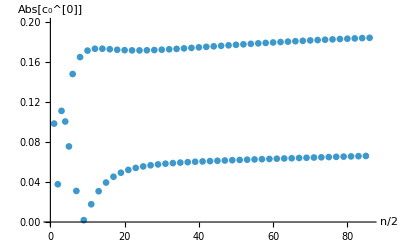

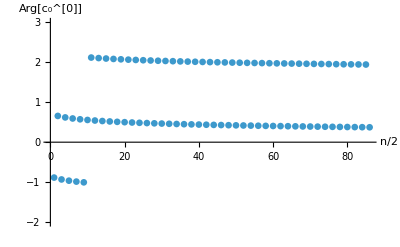

```mathematica
ps=0.012;
c00tabplotabs=ListPlot[Table[{n,c00tab[[n,1]]},{n,Length[c00tab]}],PlotRange->{{0,Length[c00tab]},{0.0,0.2}},AxesLabel->{"n/2","Abs[c_0^[0]]"},BaseStyle->Directive[FontSize->15],PlotStyle->{PointSize[ps]}]
c00tabplotangle=ListPlot[Table[{n,c00tab[[n,2]]},{n,Length[c00tab]}],PlotRange->{{0,Length[c00tab]},{-2,3}},AxesLabel->{"n/2","Arg[c_0^[0]]"},BaseStyle->Directive[FontSize->15],PlotStyle->{PointSize[ps]}]
```

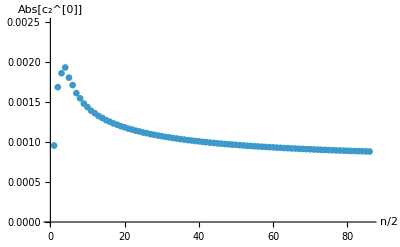

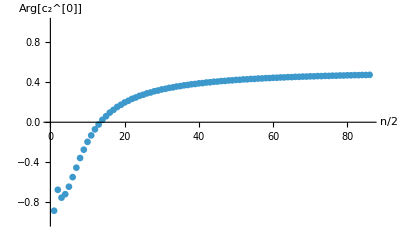

```mathematica
c20tabplotabs=ListPlot[Table[{n,c20tab[[n,1]]},{n,Length[c20tab]}],PlotRange->{{0,Length[c20tab]},{0,0.0025}},AxesLabel->{"n/2","Abs[c_2^[0]]"},BaseStyle->Directive[FontSize->15],PlotStyle->{PointSize[ps]}]
c20tabplotangle=ListPlot[Table[{n,c20tab[[n,2]]},{n,Length[c20tab]}],PlotRange->{{0,Length[c20tab]},{-1,1}},AxesLabel->{"n/2","Arg[c_2^[0]]"},BaseStyle->Directive[FontSize->15],PlotStyle->{PointSize[ps]}]
```

{param_0→0.200181,param_1→-0.817564,param_2→6.30324}

{param_0→0.0760281,param_1→-0.53004,param_2→4.39198}

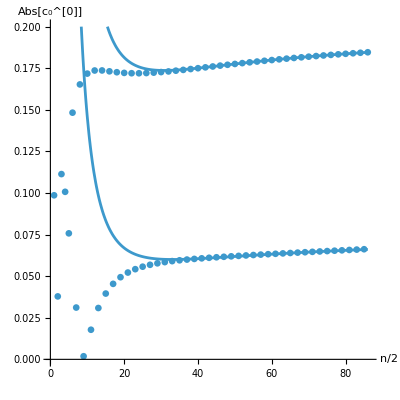

```mathematica
c00funabs=Subscript[param, 0]+Subscript[param, 1]/n+Subscript[param, 2]/n^2;
parameters={Subscript[param, 0],Subscript[param, 1],Subscript[param, 2]};
fitpar=FindFit[Table[{n,c00tab[[2*n,1]]},{n,20,Floor[Length[c00tab]/2]}],c00funabs,parameters,n]
fitplot1=Plot[c00funabs/.fitpar/.n->m/2,{m,0,Length[c00tab]},PlotRange->{{0,Length[c00tab]+0.5},{0,0.2}},BaseStyle->Directive[FontSize->15],AspectRatio->1];
fitpar=FindFit[Table[{n,c00tab[[2*n-1,1]]},{n,20,Floor[Length[c00tab]/2]}],c00funabs,parameters,n]
fitplot2=Plot[c00funabs/.fitpar/.n->m/2,{m,0,Length[c00tab]},PlotRange->{{0,Length[c00tab]+0.5},{0,0.2}},BaseStyle->Directive[FontSize->15],AspectRatio->1];
Show[fitplot1,fitplot2,c00tabplotabs,AxesLabel->{"n/2","Abs[c_0^[0]]"}]
```

```mathematica
(0.07602813508614076+0.20018052456039756)/16
```

0.017263

```mathematica
0.017263041227908643
```

{param_0→0.284516,param_1→4.51738,param_2→-27.1645}

{param_0→1.85531,param_1→4.56325,param_2→-27.1959}

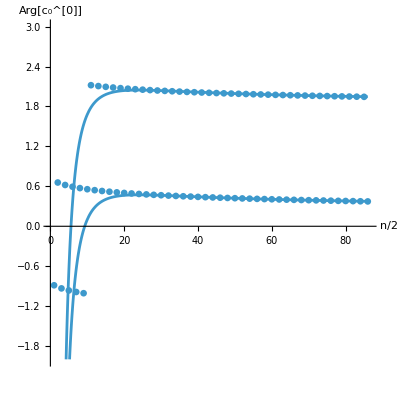

```mathematica
c00funangle=Subscript[param, 0]+Subscript[param, 1]/n+Subscript[param, 2]/n^2;
parameters={Subscript[param, 0],Subscript[param, 1],Subscript[param, 2]};
fitpar=FindFit[Table[{n,c00tab[[2*n,2]]},{n,15,Length[c00tab]/2}],c00funangle,parameters,n]
fitplot1=Plot[c00funangle/.fitpar/.n->m/2,{m,0,Length[c00tab]},PlotRange->{{0,Length[c00tab]+0.5},{-2,3}},BaseStyle->Directive[FontSize->15],AspectRatio->1];
fitpar=FindFit[Table[{n,c00tab[[2*n-1,2]]},{n,15,Length[c00tab]/2}],c00funangle,parameters,n]
fitplot2=Plot[c00funangle/.fitpar/.n->m/2,{m,0,Length[c00tab]},PlotRange->{{0,Length[c00tab]+0.5},{-2,3}},BaseStyle->Directive[FontSize->15],AspectRatio->1];
Show[fitplot1,fitplot2,c00tabplotangle,AxesLabel->{"n/2","Arg[c_0^[0]]"}]
```

{param_0→0.000763389,param_1→0.0110988,param_2→-0.052179}

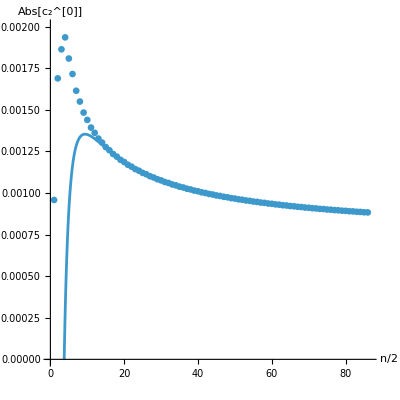

```mathematica
c20funabs=Subscript[param, 0]+Subscript[param, 1]/n+Subscript[param, 2]/n^2;
parameters={Subscript[param, 0],Subscript[param, 1],Subscript[param, 2]};
fitpar=FindFit[Table[{n,c20tab[[n,1]]},{n,15,Length[c20tab]}],c00funabs,parameters,n]
fitplot=Plot[c20funabs/.fitpar,{n,0,Length[c20tab]},PlotRange->{{0,Length[c20tab]+0.5},{0,0.002}},AxesLabel->{"n/2","Abs[c_2^[0]]"},BaseStyle->Directive[FontSize->15],AspectRatio->1];
Show[fitplot,c20tabplotabs]
```

{param_0→0.547143,param_1→-5.79373,param_2→-23.4784}

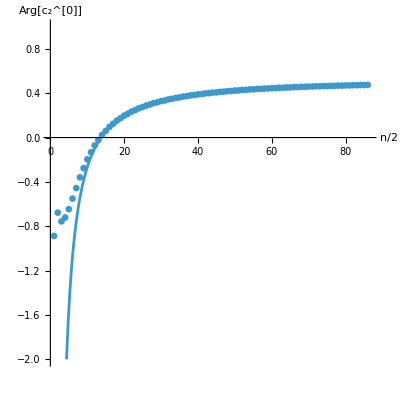

```mathematica
c20funangle=Subscript[param, 0]+Subscript[param, 1]/n+Subscript[param, 2]/n^2;
parameters={Subscript[param, 0],Subscript[param, 1],Subscript[param, 2]};
fitpar=FindFit[Table[{n,c20tab[[n,2]]},{n,15,Length[c20tab]}],c00funangle,parameters,n]
fitplot=Plot[c20funangle/.fitpar,{n,0,Length[c20tab]},PlotRange->{{0,Length[c20tab]+0.5},{-2,1}},AxesLabel->{"n/2","Arg[c_2^[0]]"},BaseStyle->Directive[FontSize->15],AspectRatio->1];
Show[fitplot,c20tabplotangle]
```